```mathematica
periodicFunction[xp_,xq_,sf_,p_,l_,mu_] := sf^2 Exp[-2*(Sin[Pi*(xp-xq)/p-mu]/l)^2]
```

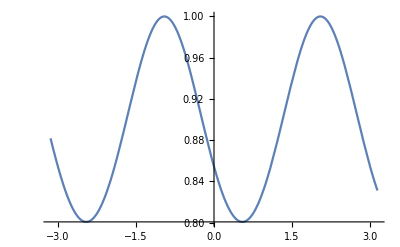

```mathematica
Plot[periodicFunction[0,x,1,3,3,1],{x,-Pi,Pi}]
```

```mathematica
FullSimplify[D[periodicFunction[xp,xq,sf,p,l,mu],sf]]
```

2 ⅇ^(-(2 Sin[mu+(π (-xp+xq))/p]^2)/l^2) sf

```mathematica
FullSimplify[D[periodicFunction[xp,xq,sf,p,l,mu],p]]
```

(2 ⅇ^(-(2 Sin[mu+(π (-xp+xq))/p]^2)/l^2) π sf^2 (-xp+xq) Sin[2 (mu+(π (-xp+xq))/p)])/(l^2 p^2)

```mathematica
FullSimplify[D[periodicFunction[xp,xq,sf,p,l,mu],l]]
```

(4 ⅇ^(-(2 Sin[mu+(π (-xp+xq))/p]^2)/l^2) sf^2 Sin[mu+(π (-xp+xq))/p]^2)/l^3

```mathematica
FullSimplify[D[periodicFunction[xp,xq,sf,p,l,mu],mu]]
```

-(2 ⅇ^(-(2 Sin[mu+(π (-xp+xq))/p]^2)/l^2) sf^2 Sin[2 (mu+(π (-xp+xq))/p)])/l^2